Autocorrelations for Generalised Hybrid Monte Carlo

## Quadratic Operators with Exponentially Distributed Trajectories

Based on the paper, “Cost of the Generalised Hybrid Monte Carlo Algorithm for Free Field Theory”, this notebook contains a Mathematica format for selected equations. The aim is to provide a dynamic method of working with the theory.

The paper provides the Laplace Transform of the autocorrelations which will be denoted by F[...] where β is the Laplace transformed time, t

Unless explicitly stated, all equations are in Laplace Transformed format

Throughout the plots, the following parameters will be used:

```mathematica
Clear[τ,r,ϕ,θ,ρ, tf, steps, dtau, traj, rate, j , k, μ, ν, pacc];
Clear[ F, rawF, Funit, FHMC, FHMCunit];
Clear[iF, iFunit,iFHMC, iFHMCunit,iFHMC, iFHMCunit];
Clear[A, Aunit, AHMC, AHMCunit];
Clear[CF, CFunit, CHMC, CHMCunit];
Clear[Cunit, Cunitn];
Clear[CFn, CFunitn, CHMCn, CHMCunitn];
Clear[tmp0, tmp1, tmp2, hmcTmp2, hmcTmp];
Clear[a0, a1, a2, a3, a4, a5, a6, a7, a8, a9];
```

## Derivation of Laplace Transformed GHMC Autocorrelation Function

```mathematica
Clear[B, g, gp, gm, gp20, gm00, gp11, gp02];
Clear[gn0, gn1, gn2, gn3, gd0, gd1, gd2, gd3];
Clear[fG, fGHMC];
```

The following functions G^+ (gp) and G^- (gm) are defined for the exponentially distributed trajectories as,

```mathematica
B[k_] := If[IntegerQ[k/2],β τ+1, (j+k-2 μ - 2 ν)ϕ];
g [j_,k_]:=Sum[Sum[Binomial[j,μ]  Binomial[k,ν]((1/2)^(j+k)(-1)^(ν+(1/2 k))B[k])/((β τ+1)^2+ϕ^2(j+k-2μ-2ν)^2), {ν, 0, k}],{μ, 0, j}];
gp[j_, k_] := ρ  g[ j,k];
gm[j_, k_] := (1-ρ)g[j,k];
```

and are used to populate the following equations to obtain the Laplace Tranformed autocorrelation functions. 
The general case is given by populating,

```mathematica
gp20= gp[2,0];
gm00 = gm[0,0];
gp11 = gp[1,1];
gp02 = gp[0,2];
```

```mathematica
gn0:=gp20+gm00;
gn1:=-gp20^2-2 gp11^2+gp02 gm00+gp02 gp20+gm00^2;
gn2:=-(gp20-gp02+gm00) (gm00+gp20+gp02);
gn3:=(gm00+gp20+gp02) (gp20^2-2 gp02 gp20+gp02^2+4 gp11^2-gm00^2);
gd0:=1-gm00-gp20;
gd1:=-(gp02 gm00-2 gp11^2+gm00^2+gp20 gp02-gm00+gp20-gp20^2-gp02);
gd2:=-(-gp20^2+gm00-2 gp20 gm00+gp02^2-gm00^2+gp20);
gd3:=2 gp11^2-gp02^3-4 gp11^2 gm00+gp02 gp20^2-gp02 gp20+gp02^2 gp20-gp02 gm00+gp20 gm00^2-gp20^3+gp20^2-gm00^2-4 gp20 gp11^2-gp20^2 gm00-4 gp11^2 gp02+gp02 gm00^2-gp02^2 gm00+gm00^3+2 gp02 gp20 gm00;
```

```mathematica
fG[β_, ϕ_, θ_,ρ_, τ_]:=Evaluate[(gn0+gn1 Cos[θ] + gn2 Cos[θ]^2+gn3 Cos[θ]^3)/(gd0+gd1 Cos[θ]+gd2 Cos[θ]^2+ gd3 Cos[θ]^3)]
```

## HMC Condition

The HMC case is given by,

```mathematica
fGHMC[β_, ϕ_,ρ_, τ_] :=Evaluate[(gp20 + gm00)/(1-gp20 - gm00)]
```

## Laplace Transformed GHMC Autocorrelation Function

The form is exceedingly long and so has been broken apart into testable segments specified by an[...],

```mathematica
a0[θ_,ρ_]:=-Cos[θ]^2+(1-2ρ)Cos[θ]+4
a1[θ_,ρ_] :=(-1+2ρ)Cos[θ]^3-3 Cos[θ]^2+(3-6ρ)Cos[θ]+6
a2[θ_,ρ_, ϕ_] :=(4ρ-2)Cos[θ]^3+((-2+2ρ)(ρ-2)ϕ^2+3-6ρ)Cos[θ] + ((4ρ-4)ϕ^2-3)Cos[θ]^2+(8-4ρ)ϕ^2+4
a3[θ_,ρ_, ϕ_] :=(4ρ-2)Cos[θ]^3+((4-4ρ)ϕ^2+3-6ρ)Cos[θ] + ((2ρ-4)ϕ^2-3)Cos[θ]^2+(8+2ρ)ϕ^2+4
a4[θ_,ρ_, ϕ_] :=(-4(-1+ρ)^2 ϕ^2-1+2ρ)Cos[θ]^3+((4ρ-4)ϕ^2-1)Cos[θ]^2+((-2+2ρ)(ρ-2)ϕ^2+1 -2ρ)Cos[θ] + (4-2ρ)ϕ^2+1
a5[θ_,ρ_, ϕ_] :=((2-2ρ)(ρ-2)ϕ^2-1+2ρ)Cos[θ]^3+(-4 ϕ^2-1)Cos[θ]^2+((-2ρ-4)(-1+ρ)ϕ^2+1-2ρ)Cos[θ]+(4ρ+4)ϕ^2+1
a6[θ_,ρ_, ϕ_] :=2ρ(-1+ρ)ϕ^2 Cos[θ]^3-2 Cos[θ]^2 ρ ϕ^2 - 2ρ(-1 + ρ)ϕ^2 Cos[θ]+2ρ ϕ^2
```

The Laplace Transform of the autocorrelation for quadratic operators is given by,

```mathematica
F[β_, ϕ_, θ_, ρ_, r_]:=(r β^4+a0[θ,ρ] r^2 β^3+(a1[θ,ρ]+(4-2ρ)ϕ^2)r^3 β^2 +a2[θ,ρ, ϕ] r^4 β+a4[θ,ρ, ϕ] r^5)/(β^5+a0[θ,ρ]r β^4+ (a1[θ,ρ]+4 ϕ^2)r^2 β^3 +a3[θ,ρ, ϕ] r^3 β^2+ a5[θ,ρ, ϕ] r^4 β + a6[θ,ρ, ϕ] r^5)
```

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
a7[θ_]:=-Cos[θ]+2-Cos[θ]^2
a8[θ_]:=Cos[θ]^3-Cos[θ]^2-Cos[θ]+1
```

```mathematica
Funit[β_, ϕ_, θ_, r_]:=(β^2 r+ β r^2 a7[θ] +r^3(Cos[θ]^3-Cos[θ]^2-Cos[θ]+2 ϕ^2+1))/(β^3+β^2 r a7[θ]+β r^2(a8[θ]+4 ϕ^2)+r^3(-2 Cos[θ]^2 ϕ^2+2 ϕ^2))
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMC[β_,ϕ_, ρ_, r_]:= (β^2 r+ 2 r^2 β +  ϕ^2(4-2ρ)r^3 +r^3)/(β^3+2r β^2+(4 ϕ^2+1)r^2 β+2 r^3 ϕ^2 ρ)
```

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
FHMCunit[β_, ϕ_, r_] :=(β^2 r+ 2β r^2 +2 r^3 ϕ^2+r^3)/(β^3+2 β^2 r+β r^2(1+4 ϕ^2)+r^3 2 ϕ^2)
```

## Regular GHMC Integrated Autocorrelation Function

The integrated autocorrelation for GHMC is obtained by setting β = 0 for the autocorrelation in Equation (1). As it no longer contains a dependancy upon β, this is also equivalent to the Inverse Laplace Transform i.e. the non-Transformed Integrated Autocorrelation Function,

```mathematica
A[ϕ_, θ_, ρ_]:=a4[θ,ρ, ϕ]/a6[θ,ρ, ϕ]
```

### Unit Acceptance

Under unit acceptance, ρ=1 the Laplace Transformed Autocorrelation is given by,

```mathematica
Aunit[ϕ_, θ_]:=-(Cos[θ]^3-Cos[θ]^2-Cos[θ]+2 ϕ^2+1)/(2 ϕ^2(Cos[θ]^2-1))
```

## HMC Condition

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMC[ϕ_, ρ_]:=(2-ρ)/ρ+1/(2ρ ϕ^2)
```

### HMC with Unit Acceptance

The GHMC form can be verified by comparing to the HMC form given below,

```mathematica
AHMCunit[ϕ_] :=1+1/(2 ϕ^2)
```

Check This should be equal to Equation (1) for θ=π/2, β=0 and ρ=1:

```mathematica
FullSimplify[AHMCunit[ϕ]==F[0, ϕ, π/2, 1, r]]
```

True

## Inverse Laplace Transforms: Regular GHMC Autocorrelations

Inverting the autocorrelation functions gets very messy and so starting in reverse order now makes more sense, leaving the most complicated for last.

There is a sepcific method provided in the paper however, partial fraction decomposition is not well supported in Mathematica so it makes more sense to simply force the result for those that are not immediately obvious.

## HMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMCunit = InverseLaplaceTransform[FHMCunit[β ,ϕ, r],β,t] //ToRadicals;
CHMCunit[t_, ϕ_,r_ ] := Evaluate[iFHMCunit]
CHMCunitn[t_, ϕ_,r_ ] := CHMCunit[t, ϕ,r]/CHMCunit[0, ϕ,r ]
```

### HMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFHMC = InverseLaplaceTransform[FHMC[β ,ϕ,  ρ, r],β,t] //ToRadicals ;
CHMC[t_, ϕ_, ρ_, r_ ] := Evaluate[iFHMC];
CHMCn[t_, ϕ_, ρ_, r_ ] :=CHMC[t, ϕ, ρ, r]/CHMC[0, ϕ, ρ, r] ;
```

## GHMC with Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

```mathematica
iFunit = InverseLaplaceTransform[Funit[β, ϕ, θ, r],β,t] //ToRadicals;
Cunit[t_, ϕ_, θ_, r_] := Evaluate[iFunit];
Cunitn[t_, ϕ_, θ_, r_] = Cunit[t, ϕ, θ, r]/Cunit[0, ϕ, θ, r];
```

### GHMC without Unit Acceptance

The following line the inverted form of the Laplace - Transformed Autocorrelation function and assigns it to a callable function,

#### Warning: Extremely large computation time!

This equation is huge and crashes Mathematica with even 8GB RAM and so the result is saved to a text file

The text file should not be opened manually as it will be about 20 MB and will also crash most text editors

Cleaning up the string with python code can reduce the total size to ~170 KB

A cleaned version can be found in theory/__CmainBody.txt

The text file is evaluated directly as python code by eval() in theory._mathematicaFunctions.expC()

```mathematica
(*iF = InverseLaplaceTransform[F[β, ϕ, θ,  ρ, r],β,t];
CF[t_, ϕ_, θ_,  ρ_, r_] := Evaluate[iF]*)
(*Export["equation.txt",ToString[CF[t, phi, theta, pa, r],FortranForm]];*)
```

## Interesting Plots

```mathematica
Clear[τ,r,ϕ,θ,ρ, tf, steps, dtau, traj, rate, j , k, μ, ν, pacc, minT, maxT];
tf = 50; (* length to plot along t-axis set as constant for each plot comparison *)
minT = -π/2 (* min angle *);
maxT = 5π/2(* max angle *);
```

## Integrated Autocorrelations

### GHMC vs. θ for fixed τ

The integrated autocorrelation under unit acceptance varying with mixing angle,

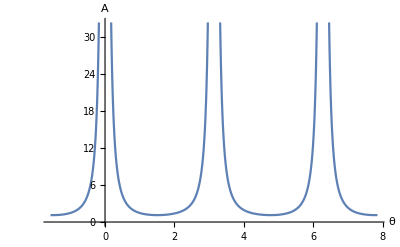

```mathematica
Clear[traj, steps, dtau,θ, phi];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
Plot[Aunit[phi, θ], {θ, minT, maxT},AxesLabel->{"θ","A"}]
```

### HMC vs. ρ for fixed τ

Showing the change in the HMC integrated autocorrelation varying with acceptance rate,

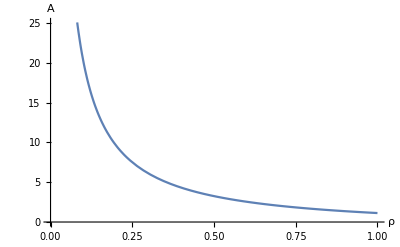

```mathematica
Clear[traj, steps, dtau,θ, phi, theta, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
theta =π/2;
Plot[A[phi, theta,ρ],{ρ, 0, 1},AxesLabel->{"ρ","A"}]
```

### HMC with Unit Acceptance vs. Ficticious Sample time, t

Plotting shows the underdamped form for unit mass and averge trajector length τ,

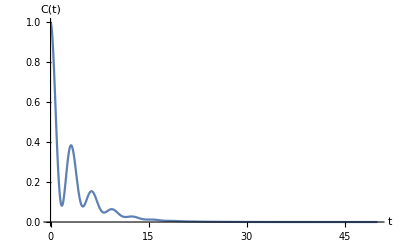

```mathematica
Clear[traj, steps, dtau, t, rate, phi, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;
Plot[CHMCunitn[t, phi, rate], {t, 0, tf},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

## Autocorrelations (Inverted Laplace Transforms)

### GHMC and HMC both with unit acceptance vs. Ficticious Sample Time, t for fixed ϕ, τ

Comparing HMC and GHMC cases,

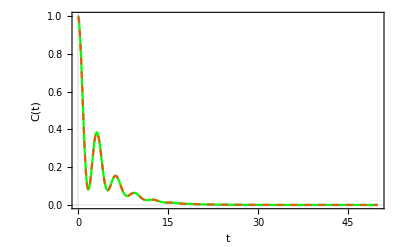

```mathematica
Clear[traj, steps, dtau, t, rate, f1, f2, phi, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;

f1 = CHMCunitn[t,phi, rate];
f2 =Cunitn[t, phi, π/2,rate];

plot1 = Plot[f1,{t,0,tf},
PlotTheme->"Scientific",PlotStyle->Green,PlotRange->{0,1},AxesLabel->{"t","C(t)"}];
plot2 =Plot[f2, {t, 0, tf},
PlotTheme->"Scientific",PlotStyle->Dashed,PlotRange->{0,1},AxesLabel->{"t","C(t)"}];
Show[plot1,plot2]
```

### HMC vs. ρ and Ficticious Sample Time, t for fixed ϕ, τ

Plotting for varying acceptance rate and smaple time,

```mathematica
Clear[traj, steps, dtau, t, ρ, rate, phi, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;

Plot3D[CHMCn[t, phi, ρ,rate], {ρ, 0, 1},{t, 0, tf}, PlotRange->{0,1},AxesLabel->{"ρ","t","C(0)"}]
```

-Graphics3D-

### HMC vs. Ficticious Sample Time, t for fixed ϕ, τ

Plotting for non unit acceptance and a small mass,

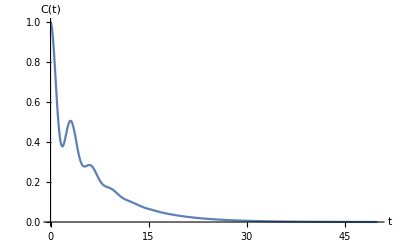

```mathematica
Clear[traj, steps, dtau, t, pacc,rate, phi, mass];
steps = 20;
dtau = 0.1;
mass = 1;
traj = steps*dtau;
phi = traj*mass;
rate = 1/traj;
pacc = 0.65;

Plot[CHMCn[t, phi,pacc, rate], {t, 0, tf},PlotRange->{0,1},AxesLabel->{"t","C(t)"}]
```

## Unit Test Results

```mathematica
Clear[bRng, thetaRng, rhoRng, phiRng, tauRng, tRng, nVars , ltSave, iacSave, iltSave, prec, zero]
```

Here are compiled a selectino of results to compare with the python implementation to verify correctness.

```mathematica
prec = 4; (* Number Precision *)
inf = 10^14; (* Inifinity threshold *)
zero = 10^-14;(* Zero threshold *)
```

#### Test Ranges

The test ranges are selected to hit key values as well as floating points that shouldn’t allow any simple cancellations,

```mathematica
bRng = { 0, 4.192};
thetaRng = {2π,0.12459};
rhoRng = { 1, 0.539};
phiRng = { 0.07, 4.79};
tauRng = {0.07, 2.7};
tRng = {0, 1, 5.79};
```

#### Save Names

The save locations for the data created to be compared to the python implementation,

```mathematica
ltSave = "__MMunittestLTexp_LT.csv"; (* laplace transform *)
iacSave="__MMunittestLTexp_iAC.csv"; (* integrated autocorrelation *)
iltSave="__MMunittestLTexp_iLT.csv";(* inverse laplace transform (autocorrelations) *)
```

## Laplace Transforms

```mathematica
Clear[ltDataset, nVars];
```

```mathematica
nVars = 5; (*Number of Function Variables: To create Table*)
```

```mathematica
ltDataset = Join[{{"beta","phi", "theta", "p_acc","tau",
 "F[beta, phi, theta, p_acc, 1/tau]",
 "fG[beta, phi, theta, p_acc, tau]"}},(*Title Line*)
Table[{β,ϕ, θ,ρ,τ, F[β,ϕ, θ,ρ, 1/τ], fG[β, ϕ, θ,ρ, τ] },(*Columns in Table*)
{β, bRng},{ϕ, phiRng}, {θ, thetaRng}, {ρ,rhoRng}, {τ, tauRng} ](*Iterate ranges. Silence errors.*)
/. x_/;NumericQ[x] :>Re[ComplexExpand[x]] (* Remove zero complex parts *)
/.x_/; Abs[Simplify[x]]> inf :> "NaN"(* replace floating point infinities *)
/.x_/; Abs[x]< zero :> 0(* replace floating point zeros *)
//N[#,prec]& (* Force number precision *)
//Flatten[#,nVars-1]&] //Quiet; (*Flatten to List. Silence Errors*)
ltDataset//Grid[#,Frame->All]&  (*Create Grid*)
```

beta | phi | theta | p_acc | tau | F[beta, phi, theta, p_acc, 1/tau] | fG[beta, phi, theta, p_acc, tau]
0 | 0.07 | 6.283 | 1. | 0.07 | NaN | NaN
0 | 0.07 | 6.283 | 1. | 2.7 | NaN | NaN
0 | 0.07 | 6.283 | 0.539 | 0.07 | NaN | NaN
0 | 0.07 | 6.283 | 0.539 | 2.7 | NaN | NaN
0 | 0.07 | 0.12459 | 1. | 0.07 | 65.5472 | 489043.
0 | 0.07 | 0.12459 | 1. | 2.7 | 65.5472 | 489043.
0 | 0.07 | 0.12459 | 0.539 | 0.07 | 186.31 | 14376.5
0 | 0.07 | 0.12459 | 0.539 | 2.7 | 186.31 | 14376.5
0 | 4.79 | 6.283 | 1. | 0.07 | NaN | NaN
0 | 4.79 | 6.283 | 1. | 2.7 | NaN | NaN
0 | 4.79 | 6.283 | 0.539 | 0.07 | NaN | NaN
0 | 4.79 | 6.283 | 0.539 | 2.7 | NaN | NaN
0 | 4.79 | 0.12459 | 1. | 0.07 | 64.7565 | 131.858
0 | 4.79 | 0.12459 | 1. | 2.7 | 64.7565 | 131.858
0 | 4.79 | 0.12459 | 0.539 | 0.07 | 66.4925 | 132.847
0 | 4.79 | 0.12459 | 0.539 | 2.7 | 66.4925 | 132.847
4.192 | 0.07 | 6.283 | 1. | 0.07 | 3.09191 | 110.807
4.192 | 0.07 | 6.283 | 1. | 2.7 | 0.088345 | 0.201484
4.192 | 0.07 | 6.283 | 0.539 | 0.07 | 3.34253 | 19.747
4.192 | 0.07 | 6.283 | 0.539 | 2.7 | 0.0883482 | 0.185727
4.192 | 0.07 | 0.12459 | 1. | 0.07 | 3.09716 | 102.28
4.192 | 0.07 | 0.12459 | 1. | 2.7 | 0.088345 | 0.200377
4.192 | 0.07 | 0.12459 | 0.539 | 0.07 | 3.34262 | 18.8105
4.192 | 0.07 | 0.12459 | 0.539 | 2.7 | 0.0883482 | 0.184835
4.192 | 4.79 | 6.283 | 1. | 0.07 | 1.70552 | 3.51909
4.192 | 4.79 | 6.283 | 1. | 2.7 | 0.0699132 | 0.154387
4.192 | 4.79 | 6.283 | 0.539 | 0.07 | 1.98715 | 3.89115
4.192 | 4.79 | 6.283 | 0.539 | 2.7 | 0.0785031 | 0.161918
4.192 | 4.79 | 0.12459 | 1. | 0.07 | 1.66196 | 3.41538
4.192 | 4.79 | 0.12459 | 1. | 2.7 | 0.0699153 | 0.15361
4.192 | 4.79 | 0.12459 | 0.539 | 0.07 | 1.95692 | 3.79373
4.192 | 4.79 | 0.12459 | 0.539 | 2.7 | 0.0785035 | 0.161179

## Integrated Autocorrelation Functions

```mathematica
Clear[iacDataset, nVars];
```

```mathematica
nVars = 4; 
iacDataset = Join[{{"phi", "theta", "p_acc", "tau",
"A[phi, theta, p_acc]", 
"F[0, phi, theta, p_acc, 1/tau]", 
"fG[0, phi, theta, p_acc, tau]"}},(*Title Line*)
Table[{ϕ, θ, ρ,τ, A[ϕ, θ, ρ],
F[0,ϕ, θ,ρ, 1/τ], 
fG[0, ϕ, θ,ρ, τ] },(*Columns in Table*)
{ϕ, phiRng}, {θ, thetaRng}, {ρ,rhoRng},{τ, tauRng}](*Iterate ranges*)
/. x_/;NumericQ[x] :>Re[ComplexExpand[x]] (* Remove zero complex parts *)
/.x_/; Abs[Simplify[x]]> inf :> "NaN"(* replace floating point infinities *)
/.x_/; Abs[x]< zero :> 0(* replace floating point zeros *)
//N[#,prec]& (* Force number precision *)
//Flatten[#,nVars-1]&] //Quiet; (*Flatten to List. Silence Errors*)
iacDataset//Grid[#,Frame->All]&  (*Create Grid.*)
```

phi | theta | p_acc | tau | A[phi, theta, p_acc] | F[0, phi, theta, p_acc, 1/tau] | fG[0, phi, theta, p_acc, tau]
0.07 | 6.283 | 1. | 0.07 | NaN | NaN | NaN
0.07 | 6.283 | 1. | 2.7 | NaN | NaN | NaN
0.07 | 6.283 | 0.539 | 0.07 | NaN | NaN | NaN
0.07 | 6.283 | 0.539 | 2.7 | NaN | NaN | NaN
0.07 | 0.12459 | 1. | 0.07 | 65.5472 | 65.5472 | 489043.
0.07 | 0.12459 | 1. | 2.7 | 65.5472 | 65.5472 | 489043.
0.07 | 0.12459 | 0.539 | 0.07 | 186.31 | 186.31 | 14376.5
0.07 | 0.12459 | 0.539 | 2.7 | 186.31 | 186.31 | 14376.5
4.79 | 6.283 | 1. | 0.07 | NaN | NaN | NaN
4.79 | 6.283 | 1. | 2.7 | NaN | NaN | NaN
4.79 | 6.283 | 0.539 | 0.07 | NaN | NaN | NaN
4.79 | 6.283 | 0.539 | 2.7 | NaN | NaN | NaN
4.79 | 0.12459 | 1. | 0.07 | 64.7565 | 64.7565 | 131.858
4.79 | 0.12459 | 1. | 2.7 | 64.7565 | 64.7565 | 131.858
4.79 | 0.12459 | 0.539 | 0.07 | 66.4925 | 66.4925 | 132.847
4.79 | 0.12459 | 0.539 | 2.7 | 66.4925 | 66.4925 | 132.847

## Inverse Laplace Transforms

```mathematica
Clear[iltDataset, nVars];
```

Instead of wasting time inverting the entire function, values are set as constants beforehand,

```mathematica
nVars = 5; (*Number of Function Variables: To create Table*)
iltDataset = Join[{{"t","tau","phi","theta","p_acc",
 "invL[F[beta, phi, theta, p_acc, 1/tau]](t)",
 "invL[fG[beta, phi, theta, p_acc, tau]](t)"}},(*Title Line*)
Table[{t,τ , ϕ, θ,ρ,
InverseLaplaceTransform[F[β, ϕ, θ,  ρ, 1/τ],β,t], 
InverseLaplaceTransform[fG[β, ϕ, θ,ρ, τ],β,t]//Re},(*Columns in Table*)
{t, tRng},{τ, tauRng},{ϕ, phiRng},{θ, thetaRng}, {ρ,rhoRng} ] (*Iterate ranges*)
/. x_/;NumericQ[x] :>Re[ComplexExpand[x]] (* Remove zero complex parts *)
/.x_/; Abs[Simplify[x]]> inf :> "NaN"(* replace floating point infinities *)
/.x_/; Abs[x]< zero :> 0(* replace floating point zeros *)
//N[#,prec]& (* Force number precision *)
//Flatten[#,nVars-1]&] //Quiet; (*Flatten to List. Silence Errors*)
iltDataset//Grid[#,Frame->All]&  (*Create Grid.*)
```

t | tau | phi | theta | p_acc | invL[F[beta, phi, theta, p_acc, 1/tau]](t) | invL[fG[beta, phi, theta, p_acc, tau]](t)
0 | 0.07 | 0.07 | 6.283 | 1. | 14.2857 | 28.5714
0 | 0.07 | 0.07 | 6.283 | 0.539 | 14.2857 | 28.5714
0 | 0.07 | 0.07 | 0.12459 | 1. | 14.2857 | 28.4608
0 | 0.07 | 0.07 | 0.12459 | 0.539 | 14.2857 | 28.4607
0 | 0.07 | 4.79 | 6.283 | 1. | 14.2857 | 28.5714
0 | 0.07 | 4.79 | 6.283 | 0.539 | 14.2857 | 28.5714
0 | 0.07 | 4.79 | 0.12459 | 1. | 14.2857 | 28.4607
0 | 0.07 | 4.79 | 0.12459 | 0.539 | 14.2857 | 28.4607
0 | 2.7 | 0.07 | 6.283 | 1. | 0.37037 | 0.740743
0 | 2.7 | 0.07 | 6.283 | 0.539 | 0.37037 | 0.740741
0 | 2.7 | 0.07 | 0.12459 | 1. | 0.37037 | 0.73787
0 | 2.7 | 0.07 | 0.12459 | 0.539 | 0.37037 | 0.73787
0 | 2.7 | 4.79 | 6.283 | 1. | 0.37037 | 0.740741
0 | 2.7 | 4.79 | 6.283 | 0.539 | 0.37037 | 0.740741
0 | 2.7 | 4.79 | 0.12459 | 1. | 0.37037 | 0.73787
0 | 2.7 | 4.79 | 0.12459 | 0.539 | 0.37037 | 0.73787
1. | 0.07 | 0.07 | 6.283 | 1. | 4.17038 | 3837.15
1. | 0.07 | 0.07 | 6.283 | 0.539 | 12.8894 | 253.214
1. | 0.07 | 0.07 | 0.12459 | 1. | 4.42488 | 3374.89
1. | 0.07 | 0.07 | 0.12459 | 0.539 | 12.8895 | 225.455
1. | 0.07 | 4.79 | 6.283 | 1. | 8.54696 | 14.5963
1. | 0.07 | 4.79 | 6.283 | 0.539 | 7.14489 | 14.5021
1. | 0.07 | 4.79 | 0.12459 | 1. | 7.64367 | 13.0178
1. | 0.07 | 4.79 | 0.12459 | 0.539 | 6.48964 | 12.9876
1. | 2.7 | 0.07 | 6.283 | 1. | 0.370121 | 1.20239
1. | 2.7 | 0.07 | 6.283 | 0.539 | 0.370244 | 0.899265
1. | 2.7 | 0.07 | 0.12459 | 1. | 0.370122 | 1.1909
1. | 2.7 | 0.07 | 0.12459 | 0.539 | 0.370244 | 0.892535
1. | 2.7 | 4.79 | 6.283 | 1. | 0.0150947 | 0.012529
1. | 2.7 | 4.79 | 6.283 | 0.539 | 0.175316 | 0.32369
1. | 2.7 | 4.79 | 0.12459 | 1. | 0.0149349 | 0.0123672
1. | 2.7 | 4.79 | 0.12459 | 0.539 | 0.175265 | 0.321836
5.79 | 0.07 | 0.07 | 6.283 | 1. | 11.0837 | 8.97428×10^6
5.79 | 0.07 | 0.07 | 6.283 | 0.539 | 8.95158 | 1146.73
5.79 | 0.07 | 0.07 | 0.12459 | 1. | 5.44795 | 4.66646×10^6
5.79 | 0.07 | 0.07 | 0.12459 | 0.539 | 8.42475 | 642.734
5.79 | 0.07 | 4.79 | 6.283 | 1. | 12.5058 | 14.6039
5.79 | 0.07 | 4.79 | 6.283 | 0.539 | 7.14286 | 14.5005
5.79 | 0.07 | 4.79 | 0.12459 | 1. | 6.6042 | 7.67981
5.79 | 0.07 | 4.79 | 0.12459 | 0.539 | 3.83869 | 7.68411
5.79 | 2.7 | 0.07 | 6.283 | 1. | 0.362087 | 4.77838
5.79 | 2.7 | 0.07 | 6.283 | 0.539 | 0.367234 | 1.65107
5.79 | 2.7 | 0.07 | 0.12459 | 1. | 0.362133 | 4.64126
5.79 | 2.7 | 0.07 | 0.12459 | 0.539 | 0.367239 | 1.6138
5.79 | 2.7 | 4.79 | 6.283 | 1. | 0.162387 | 0.420856
5.79 | 2.7 | 4.79 | 6.283 | 0.539 | 0.211216 | 0.419157
5.79 | 2.7 | 4.79 | 0.12459 | 1. | 0.160014 | 0.41212
5.79 | 2.7 | 4.79 | 0.12459 | 0.539 | 0.209704 | 0.411802

## Export Data to CSV

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export[ltSave,ltDataset,"CSV",CharacterEncoding->"UTF8"]
Export[iacSave,iacDataset,"CSV",CharacterEncoding->"UTF8"]
Export[iltSave,iltDataset,"CSV",CharacterEncoding->"UTF8"]
```

__MMunittestLTexp_LT.csv

__MMunittestLTexp_iAC.csv

__MMunittestLTexp_iLT.csv

## Formula Validations

```mathematica
Clear[getNumerator, getDenominator, flip, fullVerify, maxSimplify, quickVerify];
flip[bool_] :=If[bool, -1, 1]
getNumerator[func_, flipSign_:False, wait_:3]:=Collect[
flip[flipSign]*Numerator[TimeConstrained[func//FullSimplify, wait, Together[func]]],
{β,r,Cos[θ],ϕ, ρ}]//TraditionalForm
getDenominator[func_, flipSign_:False, wait_:3]:=Collect[
flip[flipSign]*Denominator[TimeConstrained[func//FullSimplify, wait, Together[func]]],
{β,r,Cos[θ],ϕ,ρ}]//TraditionalForm
maxSimplify[func_]:=getNumerator[func]/getDenominator[func];
```

This function verifies that two expressions are equal. If it cannot do within the initial time period, it will try a faster but less accurate method. If this also fails and error message is printed.

```mathematica
quickVerify[f1_, f2_, wait_:10, maxwait_:20, explicit_:False, fullSimplify_:False] :=Module[{t, output, status1, status2},
(* Try alternative method if it takes longer than wait *)
t= TimeConstrained[FullSimplify[f1== f2],wait, "Failed"];
status1 =If[StringQ[t],
If[explicit, (*Only prints out text if explicit flagged as True*)
StringForm["Failed to Simplify within ``s. Used PossibleZeroQ instead.",wait]
Null],
Null];
(* Exit calculation if it takes longer than maxwait *)
t= If[StringQ[t], TimeConstrained[PossibleZeroQ[n1== n2],maxwait-wait, "Failed"], t];
status2=If[StringQ[t],
If[explicit,(*Only prints out text if explicit flagged as True*)
StringForm["Failed to determine solution within maxwait of ``s. Exited.",maxwait], 
Null]
Null];
output=If[SameQ[t,True], 
{status1, status2, t//VerificationTest},(*Just output test result if passed*)
{status1, status2,t//VerificationTest,
"First Function", If[fullSimplify, f1 // FullSimplify, f1],
"Second Function", If[fullSimplify, f2 // FullSimplify, f2]}(*Outputs numerator, denominator if test fails*)
];
Print[Column[DeleteCases[output, Null]]];
]
```

This function implements quickVerify to the numerator and denominator separately,

```mathematica
fullVerify[f1_, f2_,  flipSign_:False,quotientWait_:5,wait_:10, maxwait_:20] :=Module[{n1, n2, d1, d2},
Print["Testing Numerators..."];
Print["... Getting first numerator"];
n1 =getNumerator[f1, flipSign, quotientWait];
Print["... Getting second numerator"];
n2 =getNumerator[f2, False, quotientWait];
Print["... Verifying"];
quickVerify[n1, n2, wait, maxwait, True];
Print["Testing Denominators..."];
Print["... Getting first denominator"];
d1 = getDenominator[f1, flipSign, quotientWait];
Print["... Getting second denominator"];
d2 = getDenominator[f2, False,quotientWait];
Print["... Verifying"];
quickVerify[d1, d2, wait, maxwait, True];
]
```

This section contains calidations to verify the correctness of various results.

## Derivation of Laplace Transform

To verify the form of the equation was copied correctly I copied it all out directly from the paper a few days later

```mathematica
AllTrue[
{FullSimplify[gn0==gp20+gm00],
FullSimplify[gn1==-gp20^2-2 gp11^2+gp02 gm00+gp02 gp20 + gm00^2],
FullSimplify[gn2 == -(gp20-gp02+gm00)(gm00+gp20+gp02)],
FullSimplify[gn3==(gm00+gp20+gp02)(gp20^2-2gp02 gp20 +gp02^2+4 gp11^2-gm00^2)],
FullSimplify[gd0 == 1-gm00-gp20],
FullSimplify[gd1 == -(-gp02-gp20^2+gp20-gm00+gp02 gp20 + gm00^2-2 gp11^2+gp02 gm00)], (* Did this one backwards for extra check *)
FullSimplify[gd2 == -(-gp20^2 +gm00 - 2 gp20 gm00 + gp02^2-gm00^2+gp20)], (* I'm not doing them all backwards - that was mentally draining... *)
FullSimplify[gd3 == 2 gp11^2-gp02^3-4 gp11^2 gm00+gp02 gp20^2-gp02 gp20 + gp02^2 gp20 -gp02 gm00 +gp20 gm00^2-gp20^3+gp20^2-gm00^2-4gp20 gp11^2-gp20^2 gm00-4 gp11^2 gp02+gp02 gm00^2 - gp02^2 gm00+ gm00^3+2gp02 gp20 gm00]}
,If[#,True, False]&]//VerificationTest
```

TestResultObject[…]

### HMC condition

vs. Full Derived Form

```mathematica
quickVerify[fGHMC[β, ϕ,ρ, τ],fG[β, ϕ,π/2,ρ, τ]]
```

TestResultObject[…]

## Laplace Transform

vs. Full Derived Form

```mathematica
f1=fG[β,ϕ,θ,ρ,1/r];
f2= F[β,ϕ,θ,ρ, r];
fullVerify[f1,f2];
```

Testing Numerators...

... Getting first numerator

... Getting second numerator

... Verifying

Null Failed to Simplify within 10s. Used PossibleZeroQ instead.
TestResultObject[…]
First Function
r^7 (cos^3(θ) ((-16 ρ^2+32 ρ-16) ϕ^4+(-12 ρ^2+16 ρ-8) ϕ^2+2 ρ-1)+cos(θ) ((8 ρ^2-24 ρ+16) ϕ^4+(6 ρ^2-14 ρ+8) ϕ^2-2 ρ+1)+cos^2(θ) ((16 ρ-16) ϕ^4+(4 ρ-8) ϕ^2-1)+(16-8 ρ) ϕ^4+(8-2 ρ) ϕ^2+1)+β r^6 (cos^3(θ) ((-24 ρ^2+32 ρ-16) ϕ^2+8 ρ-4)+cos(θ) ((8 ρ^2-24 ρ+16) ϕ^4+(18 ρ^2-42 ρ+24) ϕ^2-10 ρ+5)+cos^2(θ) ((16 ρ-16) ϕ^4+(12 ρ-24) ϕ^2-5)+(32-16 ρ) ϕ^4+(32-8 ρ) ϕ^2+6)+β^2 r^5 (cos^3(θ) ((-12 ρ^2+16 ρ-8) ϕ^2+12 ρ-6)+cos(θ) ((18 ρ^2-42 ρ+24) ϕ^2-20 ρ+10)+cos^2(θ) ((12 ρ-24) ϕ^2-10)+(16-8 ρ) ϕ^4+(48-12 ρ) ϕ^2+15)+β^3 r^4 (cos(θ) ((6 ρ^2-14 ρ+8) ϕ^2-20 ρ+10)+cos^2(θ) ((4 ρ-8) ϕ^2-10)+(8 ρ-4) cos^3(θ)+(32-8 ρ) ϕ^2+20)+β^4 r^3 ((2 ρ-1) cos^3(θ)+(5-10 ρ) cos(θ)-5 cos^2(θ)+(8-2 ρ) ϕ^2+15)+β^5 r^2 ((1-2 ρ) cos(θ)-cos^2(θ)+6)+β^6 r
Second Function
r^5 (cos^3(θ) ((-4 ρ^2+8 ρ-4) ϕ^2+2 ρ-1)+cos(θ) ((2 ρ^2-6 ρ+4) ϕ^2-2 ρ+1)+cos^2(θ) ((4 ρ-4) ϕ^2-1)+(4-2 ρ) ϕ^2+1)+β r^4 (cos(θ) ((2 ρ^2-6 ρ+4) ϕ^2-6 ρ+3)+cos^2(θ) ((4 ρ-4) ϕ^2-3)+(4 ρ-2) cos^3(θ)+(8-4 ρ) ϕ^2+4)+β^2 r^3 ((2 ρ-1) cos^3(θ)+(3-6 ρ) cos(θ)-3 cos^2(θ)+(4-2 ρ) ϕ^2+6)+β^3 r^2 ((1-2 ρ) cos(θ)-cos^2(θ)+4)+β^4 r

Testing Denominators...

... Getting first denominator

... Getting second denominator

... Verifying

Null Failed to Simplify within 10s. Used PossibleZeroQ instead.
TestResultObject[…]
First Function
β^7+r^7 (cos^3(θ) ((8 ρ^2-8 ρ) ϕ^4+(6 ρ^2-2 ρ) ϕ^2)+cos(θ) ((8 ρ-8 ρ^2) ϕ^4+(2 ρ-6 ρ^2) ϕ^2)+cos^2(θ) (-8 ρ ϕ^4-2 ρ ϕ^2)+8 ρ ϕ^4+2 ρ ϕ^2)+β r^6 (cos^3(θ) ((-8 ρ^2+24 ρ-16) ϕ^4+(6 ρ^2+10 ρ-8) ϕ^2+2 ρ-1)+cos(θ) ((-8 ρ^2-8 ρ+16) ϕ^4+(-18 ρ^2-6 ρ+8) ϕ^2-2 ρ+1)+cos^2(θ) ((-4 ρ-8) ϕ^2-16 ϕ^4-1)+(16 ρ+16) ϕ^4+(8 ρ+8) ϕ^2+1)+β^2 r^5 (cos^3(θ) ((-6 ρ^2+26 ρ-16) ϕ^2+8 ρ-4)+cos(θ) ((-18 ρ^2-30 ρ+24) ϕ^2+(16-16 ρ) ϕ^4-10 ρ+5)+cos^2(θ) ((8 ρ-16) ϕ^4-24 ϕ^2-5)+(8 ρ+32) ϕ^4+(12 ρ+32) ϕ^2+6)+β^3 r^4 (cos^3(θ) ((-6 ρ^2+14 ρ-8) ϕ^2+12 ρ-6)+cos(θ) ((-6 ρ^2-34 ρ+24) ϕ^2-20 ρ+10)+cos^2(θ) ((4 ρ-24) ϕ^2-10)+(8 ρ+48) ϕ^2+16 ϕ^4+15)+β^4 r^3 (cos^2(θ) ((2 ρ-8) ϕ^2-10)+cos(θ) ((8-12 ρ) ϕ^2-20 ρ+10)+(8 ρ-4) cos^3(θ)+(2 ρ+32) ϕ^2+20)+β^5 r^2 ((2 ρ-1) cos^3(θ)+(5-10 ρ) cos(θ)-5 cos^2(θ)+8 ϕ^2+15)+β^6 r ((1-2 ρ) cos(θ)-cos^2(θ)+6)
Second Function
β^5+r^5 ((2 ρ^2-2 ρ) ϕ^2 cos^3(θ)+(2 ρ-2 ρ^2) ϕ^2 cos(θ)-2 ρ ϕ^2 cos^2(θ)+2 ρ ϕ^2)+β r^4 (cos^3(θ) ((-2 ρ^2+6 ρ-4) ϕ^2+2 ρ-1)+cos(θ) ((-2 ρ^2-2 ρ+4) ϕ^2-2 ρ+1)+(-4 ϕ^2-1) cos^2(θ)+(4 ρ+4) ϕ^2+1)+β^2 r^3 (cos^2(θ) ((2 ρ-4) ϕ^2-3)+cos(θ) ((4-4 ρ) ϕ^2-6 ρ+3)+(4 ρ-2) cos^3(θ)+(2 ρ+8) ϕ^2+4)+β^3 r^2 ((2 ρ-1) cos^3(θ)+(3-6 ρ) cos(θ)-3 cos^2(θ)+4 ϕ^2+6)+β^4 r ((1-2 ρ) cos(θ)-cos^2(θ)+4)

### Laplace Transform with Unit Acceptance

vs. Full Laplace Transform

```mathematica
quickVerify[Funit[β, ϕ, θ, r],F[β, ϕ, θ, 1, r]]
```

TestResultObject[…]

vs. Full Derived Laplace Transform

```mathematica
f1 =fG[β,ϕ,θ,1,1/r];
f2 =Funit[β, ϕ, θ, r];
fullVerify[f1,f2, False, 5, 10, 20];
```

Testing Numerators...

... Getting first numerator

... Getting second numerator

... Verifying

TestResultObject[…]
First Function
r^5 ((4 ϕ^2-1) cos^3(θ)+(4 ϕ^2+1) cos^2(θ)+cos(θ)-8 ϕ^4-6 ϕ^2-1)+β r^4 ((4 ϕ^2+3) cos^2(θ)-2 cos^3(θ)+3 cos(θ)-12 ϕ^2-4)+β^2 r^3 (-cos^3(θ)+3 cos^2(θ)+3 cos(θ)-6 ϕ^2-6)+β^3 r^2 (cos^2(θ)+cos(θ)-4)-β^4 r
Second Function
r^3 (cos^3(θ)-cos^2(θ)-cos(θ)+2 ϕ^2+1)+β r^2 (-cos^2(θ)-cos(θ)+2)+β^2 r

Testing Denominators...

... Getting first denominator

... Getting second denominator

... Verifying

Null Failed to Simplify within 5s. Used PossibleZeroQ instead.
TestResultObject[…]
First Function
-β^5+r^5 (-4 ϕ^2 cos^3(θ)+4 ϕ^2 cos(θ)+(8 ϕ^4+2 ϕ^2) cos^2(θ)-8 ϕ^4-2 ϕ^2)+β r^4 ((8 ϕ^2+1) cos^2(θ)+(8 ϕ^2+1) cos(θ)-cos^3(θ)-16 ϕ^4-12 ϕ^2-1)+β^2 r^3 ((6 ϕ^2+3) cos^2(θ)+(4 ϕ^2+3) cos(θ)-2 cos^3(θ)-18 ϕ^2-4)+β^3 r^2 (-cos^3(θ)+3 cos^2(θ)+3 cos(θ)-8 ϕ^2-6)+β^4 r (cos^2(θ)+cos(θ)-4)
Second Function
β^3+2 r^3 ϕ^2 sin^2(θ)+β r^2 (cos^3(θ)-cos^2(θ)-cos(θ)+4 ϕ^2+1)+β^2 r (-cos^2(θ)-cos(θ)+2)

### Laplace Transform with HMC Condition

vs. Laplace Transform with HMC condition - simplifications are to speed up result

```mathematica
t2 = FullSimplify[F[β,ϕ,π/2,ρ,r]== FHMC[β,ϕ, ρ, r]]//VerificationTest
```

TestResultObject[…]

vs. Derived Laplace Transform with HMC condition

```mathematica
f1 = fGHMC[β,ϕ,ρ,1/r];
f2 = FHMC[β, ϕ,ρ, r];
quickVerify[f1,f2];
```

TestResultObject[…]

#### Laplace Transform with Unit Acceptance and HMC condition

vs. Laplace Transform with Unit Acceptance

```mathematica
quickVerify[FHMCunit[β, ϕ, r ],Funit[β, ϕ, π/2,r ]]
```

```mathematica
TestResultObject[…]
```

vs. Full Laplace Transform and an enforced condition of ρ=1

```mathematica
quickVerify[FHMCunit[β, ϕ, r],F[β, ϕ, π/2, 1, r]]
```

TestResultObject[…]

## Integrated Autocorrelations

vs. Laplace Transform  for  β = 0

```mathematica
quickVerify[A[ϕ, θ, ρ] , F[0, ϕ, θ, ρ, r]]
```

TestResultObject[…]

vs. Full Derived Form for β = 0

```mathematica
fullVerify[A[ϕ, θ, ρ] , fG[0, ϕ, θ, ρ, 1/r]]
```

Testing Numerators...

... Getting first numerator

... Getting second numerator

... Verifying

Null Failed to Simplify within 10s. Used PossibleZeroQ instead.
TestResultObject[…]
First Function
-(4 ρ^2 ϕ^2)/(cos(θ)+1)-4 cos(θ) (4 (ρ-1)^2 ϕ^2-2 ρ+1)+2 (ρ-2) ρ ϕ^2 csc^2(θ/2)+16 (ρ-1) ϕ^2-4
Second Function
cos^3(θ) ((-16 ρ^2+32 ρ-16) ϕ^4+(-12 ρ^2+16 ρ-8) ϕ^2+2 ρ-1)+cos(θ) ((8 ρ^2-24 ρ+16) ϕ^4+(6 ρ^2-14 ρ+8) ϕ^2-2 ρ+1)+cos^2(θ) ((16 ρ-16) ϕ^4+(4 ρ-8) ϕ^2-1)+(16-8 ρ) ϕ^4+(8-2 ρ) ϕ^2+1

Testing Denominators...

... Getting first denominator

... Getting second denominator

... Verifying

TestResultObject[…]
First Function
(8 ρ^2-8 ρ) ϕ^2 cos(θ)-8 ρ ϕ^2
Second Function
cos^3(θ) ((8 ρ^2-8 ρ) ϕ^4+(6 ρ^2-2 ρ) ϕ^2)+cos(θ) ((8 ρ-8 ρ^2) ϕ^4+(2 ρ-6 ρ^2) ϕ^2)+cos^2(θ) (-8 ρ ϕ^4-2 ρ ϕ^2)+8 ρ ϕ^4+2 ρ ϕ^2

### Integrated Autocorrelations with Unit Acceptance

vs. Laplace Transform with unit Acceptance for β = 0

```mathematica
f1 = Aunit[ϕ, θ];
f2 = Funit[0, ϕ, θ, r];
quickVerify[f1,f2];
```

TestResultObject[…]

vs. Full Derived Form for β = 0 and ρ=1

```mathematica
fullVerify[Aunit[ϕ, θ] , fG[0, ϕ, θ, 1, 1/r]]
```

Testing Numerators...

... Getting first numerator

... Getting second numerator

... Verifying

TestResultObject[…]
First Function
8 ϕ^2 csc^2(θ)+(-2 cos(2 θ)+cos(3 θ)+2) csc^2(θ)-cot(θ) csc(θ)
Second Function
8 ϕ^4 csc^2(θ)+6 ϕ^2 csc^2(θ)+cos^3(θ) (csc^2(θ)-4 ϕ^2 csc^2(θ))+cos^2(θ) (-4 ϕ^2 csc^2(θ)-csc^2(θ))+csc^2(θ)-cot(θ) csc(θ)

Testing Denominators...

... Getting first denominator

... Getting second denominator

... Verifying

TestResultObject[…]
First Function
8 ϕ^2
Second Function
-4 ϕ^2 cos(θ)+8 ϕ^4+2 ϕ^2

### Integrated Autocorrelations with HMC Condition

vs. Laplace Transform with HMC condition

```mathematica
quickVerify[FHMC[0,ϕ, ρ, r] , AHMC[ϕ, ρ]]
```

TestResultObject[…]

vs. Full Derived Form with HMC condition for β = 0

```mathematica
quickVerify[AHMC[ϕ, ρ] , fGHMC[0,ϕ,ρ,1/r], 5, 10, True]
```

TestResultObject[…]

#### Integrated Autocorrelations with HMC condition and Unit Acceptance

vs. Laplace Transform with HMC condition and Unit Acceptance

```mathematica
quickVerify[FHMCunit[0,ϕ, r] , AHMCunit[ϕ]]
```

TestResultObject[…]

```mathematica
fullVerify[AHMCunit[ϕ] , fGHMC[0, ϕ, 1, 1/r]]
```

Testing Numerators...

... Getting first numerator

... Getting second numerator

... Verifying

TestResultObject[…]

Testing Denominators...

... Getting first denominator

... Getting second denominator

... Verifying

TestResultObject[…]

## Inverted Laplace Transforms

No tests needed as the calculation done in Mathematica is tied to the accuracy of the previous evaluations.